# Code and Figures for Paper

## Random Sampling from 𝒟(ℍ)

```mathematica
randomSimplexPoints[d_,n_]:=RandomPoint[Simplex[Table[UnitVector[d,j],{j,1,d}]],n]
randomDiagonalOperators[d_,n_]:=DiagonalMatrix/@randomSimplexPoints[d,n]

randomUnitaryOperators[d_,n_]:=RandomVariate[CircularUnitaryMatrixDistribution[d],n]
conjugate[ρList_,unitaryList_]:=(Dot[Sequence@@#]&)/@Transpose[{unitaryList,ρList,ConjugateTranspose/@unitaryList}]

randomQuantumClassicalStates[dA_,dB_,n_]:=
Module[
{rK,ρArray},

rK=randomSimplexPoints[dB,n];
ρArray=Transpose[Table[conjugate[randomDiagonalOperators[dA,n],randomUnitaryOperators[dA,n]],dB]];

Table[(∑_(k=1)^dB rK⟦i⟧⟦k⟧KroneckerProduct[ρArray⟦i⟧⟦k⟧,DiagonalMatrix[UnitVector[dB,k]]]),{i,1,n}]
]

randomClassicalStatesWithFixedAngularDistance[θ_,dA_,dB_,n_]:=
Module[
{
sourcePoints,
targetPoints,
rotationMatrices,
newPoints,
ρList,
σList
},

sourcePoints=√randomSimplexPoints[dA dB,n];
targetPoints=RandomPoint[Sphere[dA dB],n];
rotationMatrices=RotationMatrix[θ,#]&/@Transpose[{sourcePoints,targetPoints}];
newPoints=Table[rotationMatrices⟦j⟧.sourcePoints⟦j⟧,{j,1,n}];
ρList=DiagonalMatrix/@(sourcePoints^2);
σList=DiagonalMatrix/@(newPoints^2);

Transpose[{angularDistances[ρList,σList],Abs[conditionalEntropies[ρList,dA,dB]-conditionalEntropies[σList,dA,dB]]}]
]
```

## Computing Entropies and Distances

```mathematica
partialTracesA[ρList_,dA_,dB_]:=(ResourceFunction["MatrixPartialTrace"][#,1,{dA,dB}]&)/@ρList

shannonEntropy[probabilityList_]:=Total[If[PossibleZeroQ[#],0,-# Log[#]]&/@probabilityList]
vonNeumannEntropies[ρList_]:=shannonEntropy/@Eigenvalues/@ρList
conditionalEntropies[ρList_,dA_,dB_]:=vonNeumannEntropies[ρList]-vonNeumannEntropies[partialTracesA[ρList,dA,dB]]

angularDistances[ρList_,σList_]:=ArcCos/@Total/@SingularValueList/@(Dot[Sequence@@#]&)/@Transpose[{MatrixPower[#,1/2]&/@ρList,MatrixPower[#,1/2]&/@σList}]
```

## Computing the Continuity Bound

```mathematica
lipschitzConstant[d_]:=Module[{x0=ⅇ^(2+ProductLog[-2/ⅇ^2])},If[d<x0,√(8 Log[x0]/x0)√(d-1),2Log[d]]]
continuityBound[dA_,dB_,a_]:=Min[lipschitzConstant[dA]a,Log[dA]+Min[Log[dA],Log[dB]]]

plotOptions={ImageSize->Large,AxesLabel->{Style["A(ρ,σ)",12],Style["|H(A|B)_ρ-H(A|B)_σ|",12]},PlotTheme->"Scientific",TicksStyle->10,LabelStyle->{FontFamily->"LM Roman 9"},AspectRatio->1/GoldenRatio};

counterexample[{dA_,dB_}]:=
Module[
{
d=dA dB,
dM=Min[dA,dB]
},

{ArcCos[√(1-(d-1)/d λ)],Abs[-Log[dM]+(1-(d-1)/d λ)Log[1-(d-1)/d λ]+(d-1)λ/d Log[λ/d]-(dB-dM)λ/dB Log[λ/dB]-dM(λ/dB+(1-λ)/dM)Log[λ/dB+(1-λ)/dM]]}
]
```

## Classical-Quantum States

```mathematica
n=100000;
dA=2;
dB=2;
```

```mathematica
ρList=randomQuantumClassicalStates[dA,dB,n];
σList=randomQuantumClassicalStates[dA,dB,n];
data1=Transpose[{angularDistances[ρList,σList],Abs[conditionalEntropies[ρList,dA,dB]-conditionalEntropies[σList,dA,dB]]}];
```

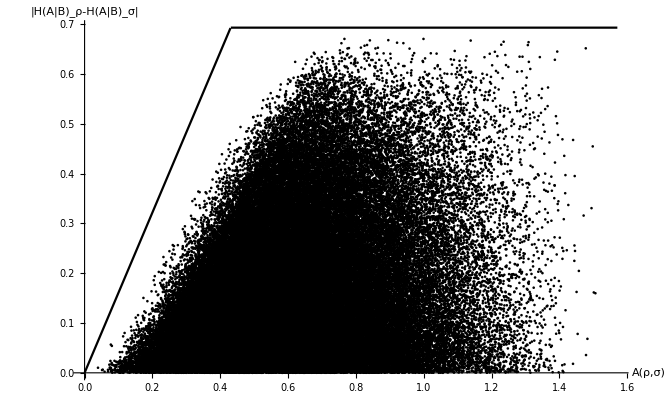

```mathematica
Show[ListPlot[data1,PlotStyle->Black],Plot[Min[lipschitzConstant[dA]a,Log[dA]],{a,0,π/2},PlotStyle->Black],Sequence@@plotOptions,PlotRange->{{0,π/2},{0,Log[dA]}}]
```

## Fixed Angular Distance

```mathematica
n=10000;
dA=2;
dB=1;
```

```mathematica
θMin=10^-5;
data2=randomClassicalStatesWithFixedAngularDistance[#,dA,dB,n]&/@(Range[10]θMin);
```

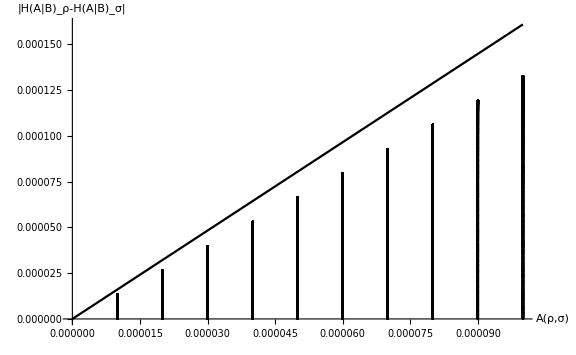

```mathematica
Show[ListPlot[data2,PlotStyle->Black],Plot[continuityBound[dA,dB,a],{a,0,10θMin},PlotStyle->Black],Sequence@@plotOptions,PlotRange->{{0,10θMin},{0,continuityBound[dA,dB,10θMin]}}]
```

```mathematica
dA=8;
dB=1;
```

```mathematica
θMin=10^-5;
data3=randomClassicalStatesWithFixedAngularDistance[#,dA,dB,n]&/@(Range[10]θMin);
```

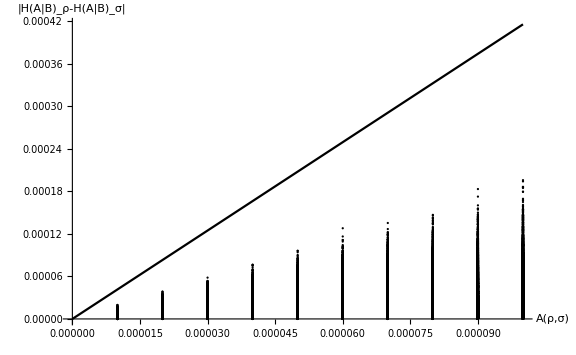

```mathematica
Show[ListPlot[data3,PlotStyle->Black],Plot[continuityBound[dA,dB,a],{a,0,10θMin},PlotStyle->Black],Sequence@@plotOptions,PlotRange->{{0,10θMin},{0,continuityBound[dA,dB,10θMin]}}]
```

## Counterexample

```mathematica
dA=2;
dB=2;
```

```mathematica
data4=counterexample[{dA,dB}];
```

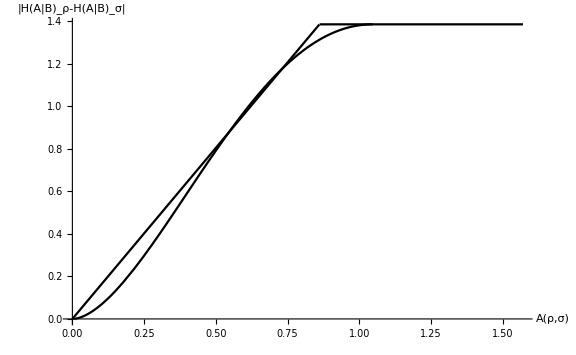

```mathematica
Show[ParametricPlot[data4,{λ,0,1},PlotStyle->Black],Plot[continuityBound[dA,dB,a],{a,0,π/2},PlotStyle->Black],Sequence@@plotOptions,PlotRange->{{0,π/2},{0,continuityBound[dA,dB,π/2]}}]
```

```mathematica
dA=8;
dB=2;
```

```mathematica
data5=counterexample[{dA,dB}];
```

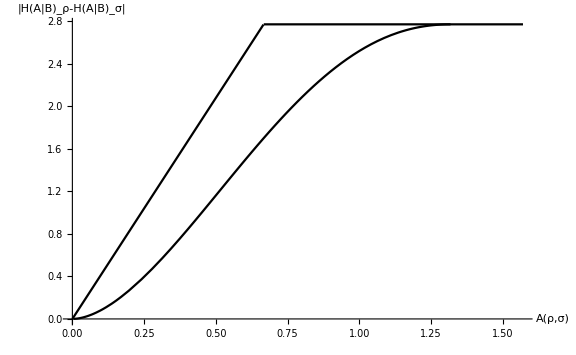

```mathematica
Show[ParametricPlot[data5,{λ,0,1},PlotStyle->Black],Plot[continuityBound[dA,dB,a],{a,0,π/2},PlotStyle->Black],Sequence@@plotOptions,PlotRange->{{0,π/2},{0,continuityBound[dA,dB,π/2]}}]
```